# GeneralizedTriangularGridGraph

Creates a triangular grid graph with customizable width and height, represented as a parallelogram composed of triangular grids

## Definition

```mathematica
ClearAll[PositiveIntegerQ]
```

```mathematica
PositiveIntegerQ[n_]:=And@@{IntegerQ[n],TrueQ[n∈PositiveIntegers]}
```

```mathematica
PositiveIntegerQ::usage="PositiveIntegerQ[n] yields True when n is a strictly positive integer. PositiveInteger[0] returns False.";
```

```mathematica
ClearAll[VertexCoordinateList]
```

```mathematica
VertexCoordinateList[g_] := GraphEmbedding[g][[Last /@ Sort[Transpose[{VertexList[g], Range[VertexCount[g]]}]]]]
```

```mathematica
ClearAll[TriangularGridGraph]
```

```mathematica
TriangularGridGraph[{wide_Integer?Positive,high_Integer?Positive},opts:OptionsPattern[Graph]]:=Module[{cells,edges,vertices},cells=Flatten[Table[CirclePoints[{Sqrt[3] (2 j+k-2),3 k-2},{2,π/2},3],{j,wide},{k,high}],1];
edges=Union[Sort/@Flatten[Partition[#,2,1,1]&/@cells,1]];
vertices=Union[Flatten[edges,1]];
IndexGraph[Graph[UndirectedEdge@@@edges,opts,VertexCoordinates->Thread[vertices->vertices]]]]
```

```mathematica
ClearAll[GeneralizedTriangularGridGraph]
```

```mathematica
GeneralizedTriangularGridGraph[input:{m_?PositiveIntegerQ,n_?PositiveIntegerQ},opts:OptionsPattern[Graph]]:=Module[{vertexCoordinates,triangularGridGraph,vertices, vertexCoordinatesToVerticesAssociation,topPartDeletedGraph,subGraph,verticesToKeep},triangularGridGraph=TriangularGridGraph[input+1](*This line creates a triangular grid graph that is slightly larger than the desired size.*);

vertexCoordinates=VertexCoordinateList[triangularGridGraph](*This line gets the coordinates of each vertex in the graph.*);

vertices=VertexList[triangularGridGraph](*This line gets a list of all vertices in the graph.*);topPartDeletedGraph=VertexDelete[triangularGridGraph,Flatten[PositionLargest[vertexCoordinates,1,Order[Last[#1],Last[#2]]&]]](*-This line removes the top part of the graph.*);
vertexCoordinatesToVerticesAssociation=AssociationThread[vertexCoordinates->vertices](*This line creates an association that maps each vertex to its coordinates.*);verticesToKeep=Lookup[vertexCoordinatesToVerticesAssociation,Catenate[Values[Most/@SortBy[First]/@GroupBy[Last][vertexCoordinates]]]](*This line determines which vertices to keep in the final graph.*);
subGraph=Subgraph[topPartDeletedGraph,verticesToKeep,opts](*This line creates a subgraph of the original graph that contains only the vertices that were determined to be kept in the previous line.*)]
GeneralizedTriangularGridGraph::usage="GeneralizedTriangularGridGraph[{width, height}] generates a triangular grid graph with the specified width and height. The width and height should be positive integers.";
```

## Documentation

### Usage

GeneralizedTriangularGridGraph[{width, height}]

generates a triangular grid graph with the specified width and height. The width and height should be positive integers.

### Details & Options

Additional information about usage and options.

## Examples

### Basic Examples

This is a triangular grid graph 4 elements wide and 3 elements tall:

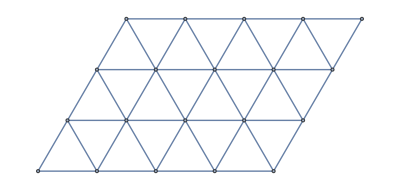

```mathematica
GeneralizedTriangularGridGraph[{4,3}]
```

This graph is 3 elements wide and 4 units tall:

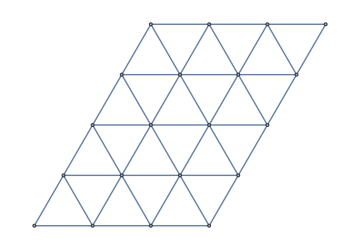

```mathematica
GeneralizedTriangularGridGraph[{3,4},ImageSize->Medium]
```

All Graph options like VertexLabels are supported:

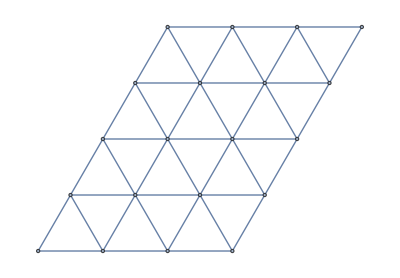

```mathematica
GeneralizedTriangularGridGraph[{3,4},VertexLabels->Placed["Name",Tooltip]]
```

### Scope

Make a grid graph of 54 by 54:

```mathematica
GeneralizedTriangularGridGraph[{54,54}]
```

-Graphics-

Make a grid graph of 57 by 57:

```mathematica
GeneralizedTriangularGridGraph[{57,57}]
```

-Graphics-

A graph of 58 by 58 will not plot:

```mathematica
GeneralizedTriangularGridGraph[{58,58}]
```

-Graphics-

I think this is because the edge count exceeds 10,000.

The output is a graph:

```mathematica
GraphQ[]
```

True

Let’s try GraphPlot:

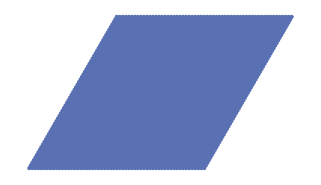

```mathematica
GraphPlot[]
```

We don’t have to use GraphPlot if we decrease the height to 30 from 58:

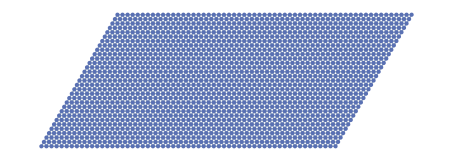

```mathematica
GeneralizedTriangularGridGraph[{58,30}]
```

### Options

All Graph options are supported.

Color the background with the option Background:

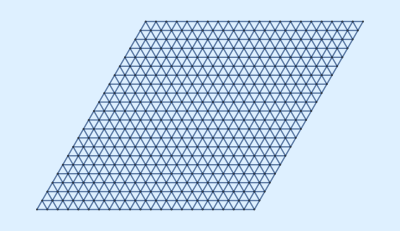

```mathematica
GeneralizedTriangularGridGraph[{21,21},Background->LightBlue]
```

Change the layout with GraphLayout:

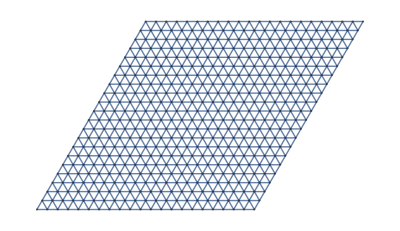

```mathematica
GeneralizedTriangularGridGraph[{21,21},GraphLayout->"GridEmbedding"]
```

```mathematica
GeneralizedTriangularGridGraph[{21,21},GraphLayout->"PlanarEmbedding"]
```

-Graphics-

Choose a vertex shape function:

Make the image large:

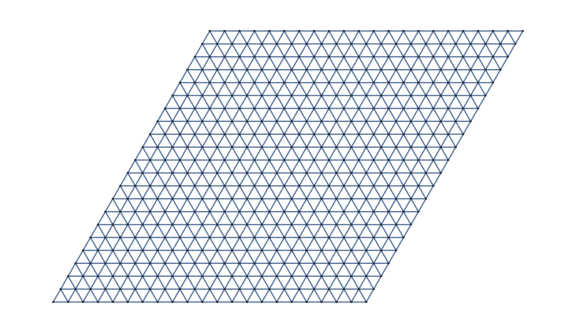

```mathematica
GeneralizedTriangularGridGraph[{21,21},ImageSize->Large]
```

Make the image full size:

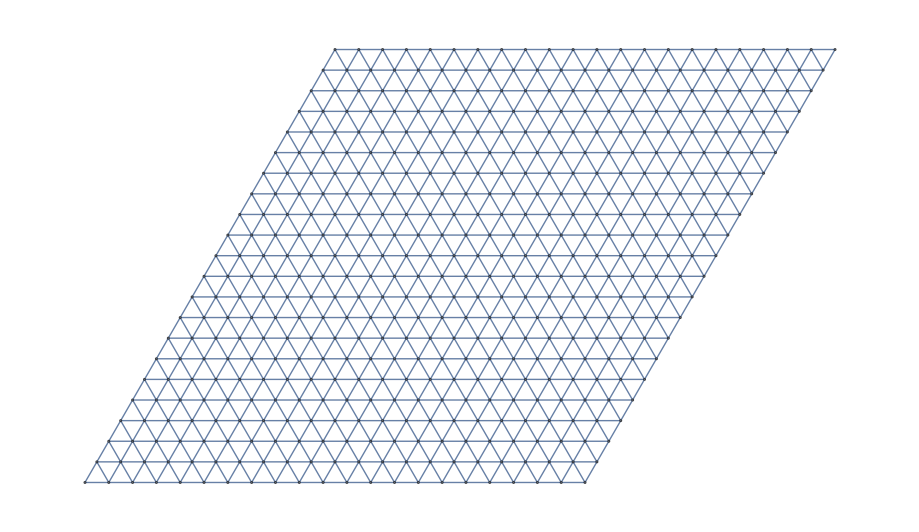

```mathematica
GeneralizedTriangularGridGraph[{21,21},ImageSize->Full]
```

#### VertexShapeFunction

Use built-in settings for VertexShapeFunctionpaclet:ref/VertexShapeFunction in the "Basic" collection:

```mathematica
ResourceData["VertexShapeFunction","Basic"]
```

{Capsule,Circle,Diamond,DownTrapezoid,FiveDown,Hexagon,Octagon,Parallelogram,Pentagon,Point,Rectangle,Square,Star,Triangle,UpTrapezoid}

Simple basic shapes:

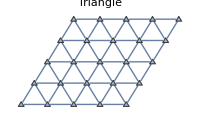
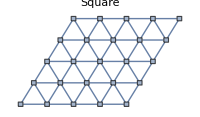
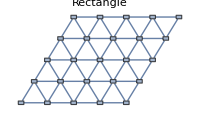
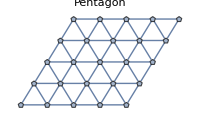
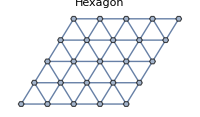
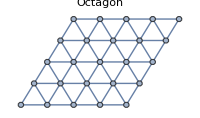

```mathematica
Table[GeneralizedTriangularGridGraph[{4,4},VertexShapeFunction->vf,VertexSize->0.2,PlotLabel->vf,ImageSize->200],{vf,{"Triangle","Square","Rectangle","Pentagon","Hexagon","Octagon"}}]
```

Common basic shapes:

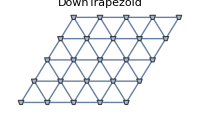
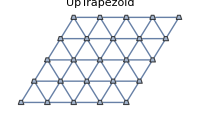
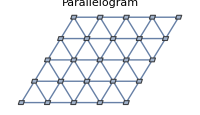
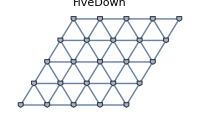
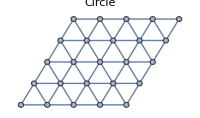
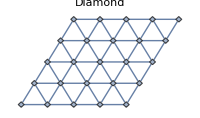
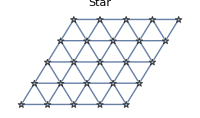
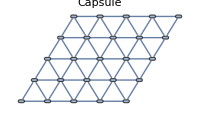

```mathematica
Table[GeneralizedTriangularGridGraph[{4,4},VertexShapeFunction->vf,VertexSize->0.2,PlotLabel->vf,ImageSize->200],{vf,{"DownTrapezoid","UpTrapezoid","Parallelogram","FiveDown","Circle","Diamond","Star","Capsule"}}]
```

Use built-in settings for VertexShapeFunctionpaclet:ref/VertexShapeFunction in the "Rounded" collection:

```mathematica
ResourceData["VertexShapeFunction","Rounded"]
```

{RoundedDiamond,RoundedDownTrapezoid,RoundedFiveDown,RoundedHexagon,RoundedParallelogram,RoundedPentagon,RoundedRectangle,RoundedSquare,RoundedTriangle,RoundedUpTrapezoid}

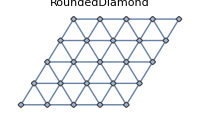
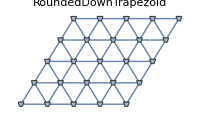
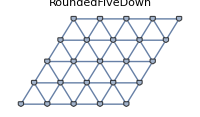
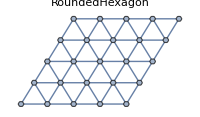
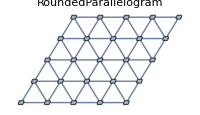
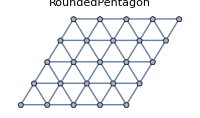
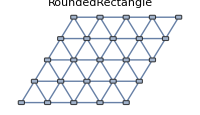
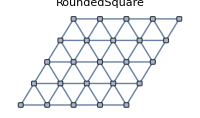

```mathematica
Table[GeneralizedTriangularGridGraph[{4,4},VertexShapeFunction->vf,VertexSize->0.2,PlotLabel->Style[vf,9],ImageSize->200],{vf,ResourceData["VertexShapeFunction","Rounded"]}]
```

Use built-in settings for VertexShapeFunctionpaclet:ref/VertexShapeFunction in the "Concave" collection:

```mathematica
ResourceData["VertexShapeFunction","Concave"]
```

{ConcaveDiamond,ConcaveHexagon,ConcavePentagon,ConcaveSquare,ConcaveTriangle}

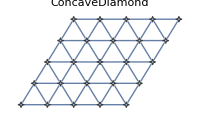
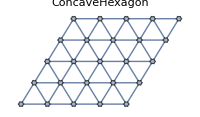
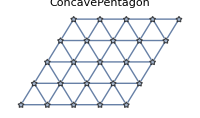
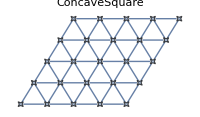
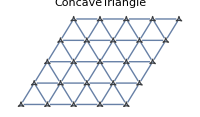

```mathematica
Table[GeneralizedTriangularGridGraph[{4,4},VertexShapeFunction->vf,VertexSize->0.2,PlotLabel->Style[vf,9],ImageSize->200],{vf,ResourceData["VertexShapeFunction","Concave"]}]
```

#### EdgeShapeFunction

Get a list of built-in settings for EdgeShapeFunctionpaclet:ref/EdgeShapeFunction:

```mathematica
ResourceData["EdgeShapeFunction"]
```

{Arrow,BoxLine,CarvedArcArrow,CarvedArrow,DashedLine,DiamondLine,DotLine,DottedLine,FilledArcArrow,FilledArrow,HalfFilledArrow,HalfFilledDoubleArrow,HalfUnfilledArrow,HalfUnfilledDoubleArrow,Line,ShortCarvedArcArrow,ShortCarvedArrow,ShortFilledArcArrow,ShortFilledArrow,ShortUnfilledArcArrow,ShortUnfilledArrow,UnfilledArcArrow,UnfilledArrow}

Undirected edges including the basic line:

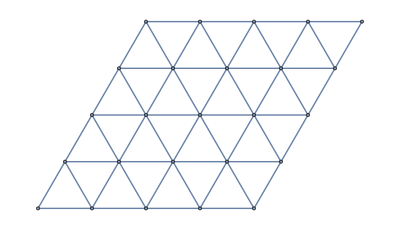

```mathematica
GeneralizedTriangularGridGraph[{4,4},EdgeShapeFunction->"Line"]
```

Lines with different glyphs on the edges:

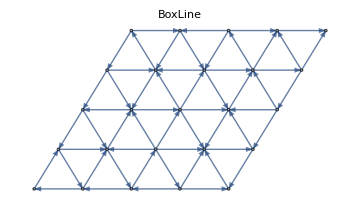
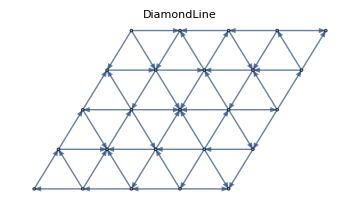
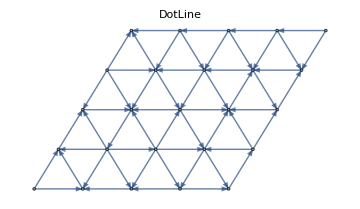

```mathematica
Table[Graph[DirectedGraph[GeneralizedTriangularGridGraph[{4,4}],"Random"],EdgeShapeFunction->{{ef,"ArrowSize"->0.05}},PlotLabel->ef,ImageSize->Medium],{ef,{"BoxLine","DiamondLine","DotLine"}}]
```

Directed edges including solid arrows:

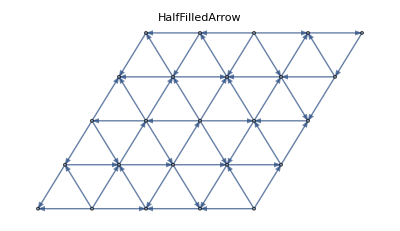
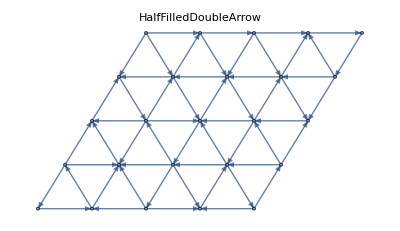
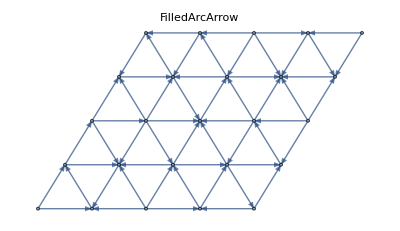
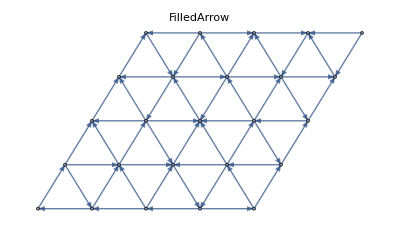
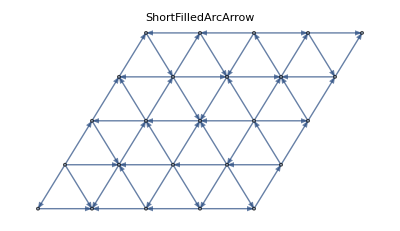
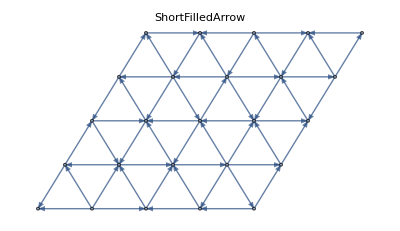

```mathematica
Table[Graph[DirectedGraph[GeneralizedTriangularGridGraph[{4,4}],"Random"],EdgeShapeFunction->{{ef,"ArrowSize"->0.1}},PlotLabel->ef],{ef,ResourceData["EdgeShapeFunction","FilledArrow"]}]
```

Line arrows:

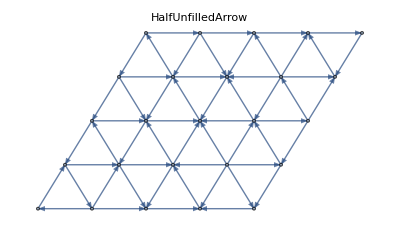
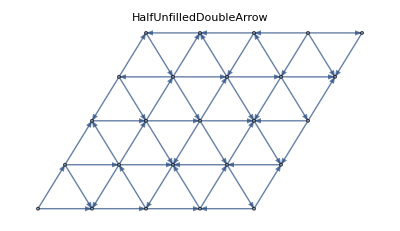
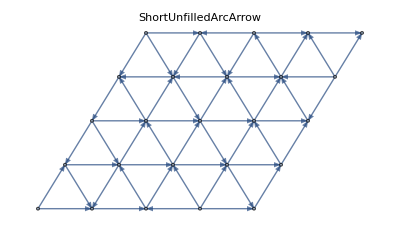
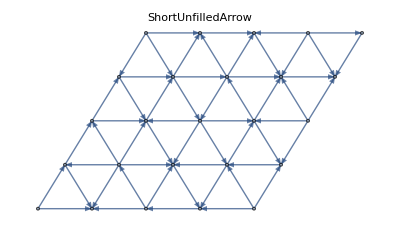
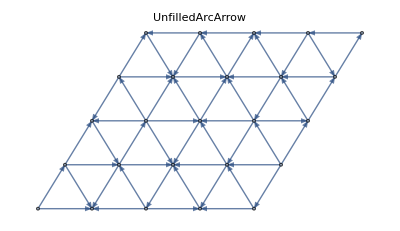
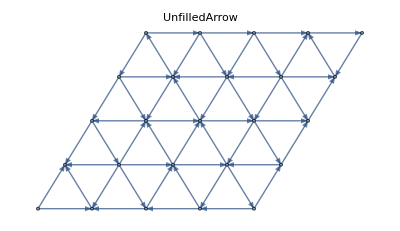

```mathematica
Table[Graph[DirectedGraph[GeneralizedTriangularGridGraph[{4,4}],"Random"],EdgeShapeFunction->{{ef,"ArrowSize"->0.1}},PlotLabel->ef],{ef,ResourceData["EdgeShapeFunction","UnfilledArrow"]}]
```

Open arrows:

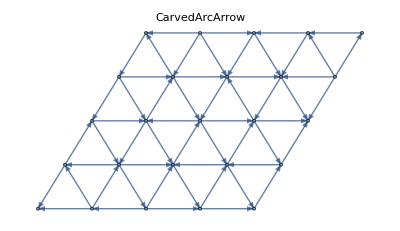
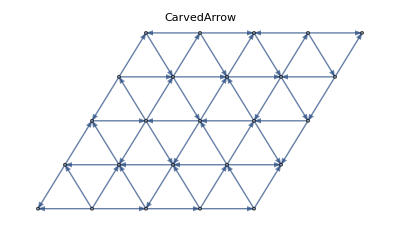
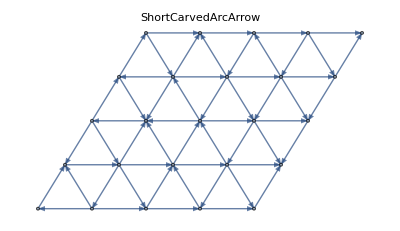
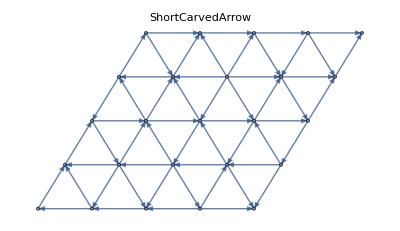

```mathematica
Table[Graph[DirectedGraph[GeneralizedTriangularGridGraph[{4,4}],"Random"],EdgeShapeFunction->{{ef,"ArrowSize"->0.1}},PlotLabel->ef],{ef,ResourceData["EdgeShapeFunction","CarvedArrow"]}]
```

### Applications

### Properties and Relations

This is similar to GridGraph:

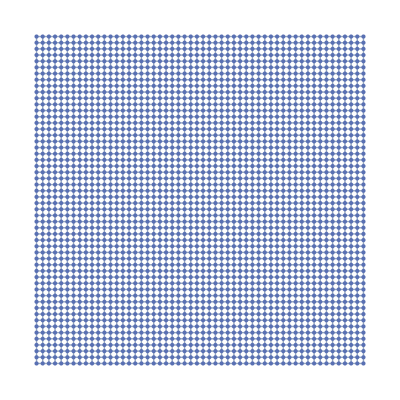

```mathematica
GridGraph[{54,54}]
```

There's also the function HexagonalGridGraph which tiles the plane with hexagons:

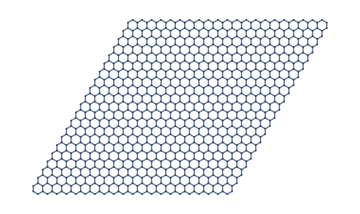

```mathematica
ResourceFunction["HexagonalGridGraph"][{21,21},ImageSize->Medium]
```

The function TriangularGridGraph does not support different height and width specifications:

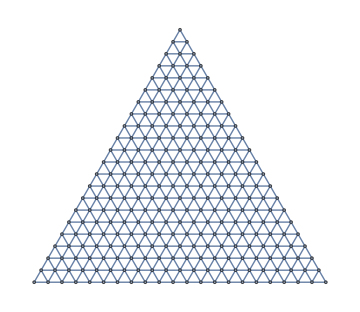

```mathematica
ResourceFunction["TriangularGridGraph"][21,ImageSize->Medium]
```

This function supports different height and width dimensions.

Make a skinny narrow tall graph:

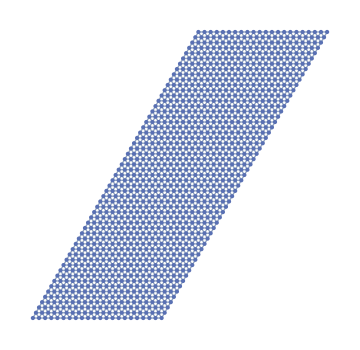

```mathematica
GeneralizedTriangularGridGraph[{21,54},ImageSize->Medium]
```

Make a short long wide graph:

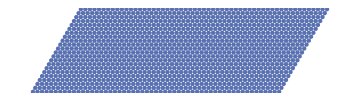

```mathematica
GeneralizedTriangularGridGraph[{54,21},ImageSize->Medium]
```

### Possible Issues

### Neat Examples

## Source & Additional Information

### Contributed By

Peter Cullen Burbery

### Keywords

Graphs

Triangles

Tilings of the plane

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

Triangle

GridGraph

Graph

CirclePoints

### Related Resource Objects

TriangularGridGraph

HexagonalGridGraph

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

13.0+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.